Walkthrough of proof of Theorem 3.1 - Adaptive Cut Selection in Mixed-Integer Linear Programming (MILP)
Cut-selection is concerned with selecting which candidate cuts to add to the LP (Linear Program. Here used as reference to the polytope of the LP relaxation of a MIP). This process often occurs at the root node (before branching on disjunctions has occurred, where branching splits the problem into two new domains), but can be performed at any stage of the solving process. This frequency is due to all cuts (alternatively called separators) generated at the root node, being globally valid for all future states of the branch and bound tree (If you’re a valid inequality for the relaxation, you’re going to also be valid for the problem who’s feasible region is a subset of the relaxation). Let us make an example of this, and use the example we are going to be using throughout this proof. Consider the following parametric mixed-integer linear program (MIP) P(a,d).
 P(a,d) =     min       x_1 - (10+d)x_2 -ax_3   
                       s.t                  -0.5 x_2+3 x_3≤ 0
                                                                -x_3 ≤  0
                                 -0.5 x_1+0.5 x_2-3.5 x_3≤ 0                
                                  0.5 x_1           + 1.5 x_3≤ 0.5         
                                  x_1,x_3 ∈ {0,1} ,   x_2 ∈ ℝ              
The valid solutions for this problem are the following, where I_X is the set of solutions:
	I_X = {(0,0,0)} ∪ {(1,x_2, 0) : ∀ x_2 ∈ [0,1]}
Because we are dealing with linear programs however, we know that if an interior point of the second set is optimal then both of the end points of the set are also optimal, so we simply take the end points of the second set and get the following set of integer feasible points:
	I_X = {(0,0,0), (1,0,0), (1,1,0)}
Let a cut be represented by α = {α_0, ..... , α_n}, where it creates the following cut:
	Σ_(1≤i≤n)α_i x_i≤α_0
A cut is therefore an inequality (we restrict ourselves to linear cuts) with the following feature:
1. It must not separate any point of I_X. (Σ_(1≤i≤n)α_i x_i^j ≤ α_0  :   ∀ x^j ∈ I_X)
A cut also often has the following property, which is not strictly necessary, but occurs nearly always:
2. Separate the LP optimal solution (This is achieved by relaxing the integrality requirements and just solving the problem). So let x^* be the LP optimal solution for the relaxation. The cut then must satisfy: Σ_(1≤i≤n)α_i(x^*)_i > α_0
The cut-selection problem then becomes deciding which subset S ⊆ S' to select, where S = {α_1, ...... , α_(|S|)} to select and add to the LP. 
SCIP, which stands for ‘Solving Constrained Integer Programs’, is a modern open-source state of the art solver that can solve MIPs. Its cut-selection routine works by scoring cuts through a parameterized weighted sum rule of four different measures. It then adds cuts, until there are no remaining cuts, or the highest score of the remaining cuts is below a threshold relative to the first cut added. The solver also ensures that no two cuts which are too parallel are added. For our proof we use a simpler form of this cut-selection rule, and focus simply on two of the four scoring measurements. Moreover, we add exactly one cut per separation round. The two scores are integer support and objective parallelism, where are defined by the scores below:
Let α be a cut as described above, and let c be the coefficients of the objective c^T x, and let J be the set of variables with integer constraints. 
		integer_support(α) = (Σ_(i ∈ J)nonzero(α_i))/(Σ_(1≤i≤n)nonzero(α_i)), where nonzero(α_i) = 0 if |α_i|=0 else 1
		objective_parallelism(α,c) = (Σ_(1≤i≤n)b_i c_i)/(√Σ_(1≤i≤n)b_i.b2√Σ_(1≤i≤n)c_i.b2)
The score of a cut α with objective c can then be written as:
		score = λ integer_support(α) + (1 - λ) objective_parallelism(α,c)       (4)

Let’s now go into the motivation now that the mathematic background is taken care of. The traditional approach for finding the value of λ that will be used in the MIP solver, is to perform a parameter sweep (most often a grid search). This experiment sets λ to multiple different values, does a large amount of tests for each value, and then selects the best performing value. For all future problems λ then does not change. Our aim is to show that this type of experiment is flawed for cut selection in MIP, and that setting a single global value for λ in the solver can be disastrous for some instances. We also want to go further, and show that no matter how you perform your parameter sweep experiment for finding the best λ value (provided it is finite), you will have disastrous results on some MIP instances when you globally set the value of λ. 
This is not entirely unexpected, as a fixed parameter cannot be expected to perform well on all possible instances, and moreover, cut selection is only a small sub-routine in the massive MIP solving process. Additionally, the instance space of MIP is non-uniform in practise, and good performance over certain problem formulations may be highly desirable as they occur more frequently. Nevertheless, we aim to show the existence of an infinite family of instances  together with an finite amount of family-wide valid cutting planes, which when using the above cut scoring rule and a pure cutting plane approach, will for all λ values in any fixed parameter sweep, not select the cuts that result in integer optimality. That is, given the parameter sweep, an infinite set of instances can be constructed that will continuously select bad cuts instead of good cuts from a pool containing both. Moreover, we show that for values of λ not contained in the parameter sweep, the good cuts would be selected and the cutting plane approach would result in integer optimal solutions. 

The larger goal of this theorem is to motivate adaptive cut selection algorithms. That is, instead of setting a global constant value of λ, make λ dependant on the problem input.

This notebook shows the calculations we did to prove each Lemma, culminating in a proof of the following theorem:
Theorem 3.1 - Given a finite discretization of λ, an infinite family of MILP instances together with an infinite amount of family-wide valid cuts can can be constructed. Using a pure cutting plane approach and applying a single cut per selection round, the infinite family of instances do not solve to optimality for any value in the discretization, but do solve to optimality for an infinite amount of alterative λ values.
For code which will directly recreate the examples and simulate the solving process, please see the python file in the same directory where this notebook was found. Now onto the proof!

Our problem  P(a,d) can be visualised as a convex hull of the following points:

```mathematica
points = {{0,0,0},{1,1,0},{1,0,0},{-1/2,3,1/2}};
ConvexHullMesh[points, MeshCellStyle->{{2,All}->Opacity[0.3, Orange]}, PlotTheme->"Detailed",AxesLabel->{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]
```

-Graphics3D-

We generate the following three cuts for solving this problem. For now assume they are valid, and that they separate the LP solution (This will be proven below).
	- The Good Cut (GC): -10 x_1+10 x_2+x_3≤0
	- The Integer Support Cut (ISC^n): -x_1+x_3<1-ϵ_n 
	- The Objective Parallelism Cut (OPC^n): -x_1+10 x_2<61/2-ϵ_n
We define ϵ_n as follows:
	0<ϵ_i<ϵ_(i+1)      ∀i∈Ν
lim_(n→∞) ϵ_n= 0.1
	
Our cut selection algorithm is designed to do the following:
- If LP solution is not integer optimal, generate candidate cuts (Those are GC, ISC^n, OPC^n).
- Apply the highest scoring cut for the given λ
- Resolve the LP and go back to the first step.

As ϵ_n is the only value that changes in the cuts, you see that the scoring of the cuts at different separation rounds is constant. This is because ϵ_n only affects the RHS value of the cuts, and the RHS value has no effect on the scoring of the cuts (go read again the definition of integer support and objective parallelism). This doesn’t mean we can ignore the RHS of course, as our cuts must still be valid cuts, but we hope that this gives insight into the direction the proof will go. As the RHS values of the cut change, and the scores remain constant, each iteration will simply apply a deeper variant of the previous cut, provided that the optimal solution isn’t found or that a deeper cut doesn’t result in an infeasible cut (These cases will be later shown to not exist in our problem). Our construction suggests by this, that no two cuts of different types will ever be applied! Please keep in mind that this a theoretical construction, and that modern solvers, even if given this exact set of separators, would recognise the redundancy, and not be trapped in an infinite loop. (The intuition here is that we need to apply an infinite amount of OPC^n or ISC^n, or simply a single GC!)

Here is the Good Cut, denoted GC.

```mathematica
Show[ConvexHullMesh[points, MeshCellStyle->{{2,All}->Opacity[0.3, Orange]}, PlotTheme->"Detailed"],Graphics3D[Hyperplane[{10,-10,-1},{1,1,0}]]]
```

-Graphics3D-

Here is the objective function visualised as hyperplane intersecting the point (1,1,0). Note that we are using parametric MILPs, and thus this is actually the objective for fixed parameters d=0 and a=4. Feel free to adjust the values and see how the objective changes!

```mathematica
Show[ConvexHullMesh[points, MeshCellStyle->{{2,All}->Opacity[0.3, Orange]}, PlotTheme->"Detailed"],Graphics3D[Hyperplane[{1,-10-0,0-4},{1,1,0}]]]
```

-Graphics3D-

The Integer Support Cut, named ISC^n. Here the cut is visualised as if ϵ_n = 0, and it does not cut off any bit of the polytope.

```mathematica
Show[ConvexHullMesh[points, MeshCellStyle->{{2,All}->Opacity[0.3, Orange]}, PlotTheme->"Detailed"],Graphics3D[Hyperplane[{1,0,-1},{-1/2,3,1/2}]]]
```

-Graphics3D-

The Objective Parallelism Cut, named OPC^n. Here the cut is visualised as if ϵ_n = 0, and it does not cut off any bit of the polytope.

```mathematica
Show[ConvexHullMesh[points, MeshCellStyle->{{2,All}->Opacity[0.3, Orange]}, PlotTheme->"Detailed"],Graphics3D[Hyperplane[{-1,10,0},{-1/2,3,1/2}]]]
```

-Graphics3D-

Lemma 3.3 - The vertex set of the LP relaxation of P(a,d), (a,d) ∈  ×[0,1],  after having applied cuts GC, ISC^n,or OPC^n are, respecitvely:
	GC_x= I_x ∪ {(61/91,60/91,10/91)}
	(ISC^n)_x=I_x ∪ {(-1/2+(3 ϵ_n)/4,3-(3 ϵ_n)/2,1/2-ϵ_n/4),(-1/2+(3 ϵ_n)/4,3-ϵ_n,1/2-ϵ_n/4),(-1/2+ϵ_n/2,3-3 ϵ_n,1/2-ϵ_n/2)}
	(OPC^n)_x=I_x ∪ {(-1/2+ϵ_n/21,3-(2 ϵ_n)/21,1/2-ϵ_n/63),(-1/2+(3 ϵ_n)/43,3-(4 ϵ_n)/43,1/2-ϵ_n/43),(-1/2+ϵ_n/61,3-(6 ϵ_n)/61,1/2-ϵ_n/61)}

We get these vertex sets by applying the cuts, and then simply calculating the new vertices made from the hyperplane intersections. Note that all cuts remove the one non integer vertex of the original convex hull, and that ISC^n and OPC^n both completely cut of the faces induced by previous iterations of their own cuts. Note that eps here represents ϵ_n. Please go back and see the visualisation of the polytope and the cuts above if this process is unintuitive!

We first do this procedure for ISC^n. We know which hyperplane intersections form the vertex set of the new face so we simply get the points in terms of the epsilon values on the RHS of the constraint.

```mathematica
intsupv1 = Solve[x1/2+(3x3)/2==1/2&&-x2/2+3*x3==0&&-1*x1+x3==1-eps,{x1,x2,x3}][[1]]
intsupv2 = Solve[x1/2+(3*x3)/2==1/2&&-x1/2+x2/2-(7x3)/2==0&&-x1+x3==1-eps,{x1,x2,x3}][[1]]
intsupv3 = Solve[-x2/2+3x3==0&&-x1/2+x2/2-(7x3)/2==0&&-x1+x3==1-eps,{x1,x2,x3}][[1]]
```

{x1→1/4 (-2+3 eps),x2→-3/2 (-2+eps),x3→(2-eps)/4}

{x1→1/4 (-2+3 eps),x2→3-eps,x3→(2-eps)/4}

{x1→1/2 (-1+eps),x2→-3 (-1+eps),x3→(1-eps)/2}

We now do the same procedure for the OPC^n

```mathematica
objparalv1 = Solve[x1/2+(3x3)/2==1/2&&-x2/2+3x3==0&&-x1+10x2==61/2-eps,{x1,x2,x3}][[1]]
objparalv2 = Solve[x1/2+(3x3)/2==1/2&&-x1/2+x2/2-(7x3)/2==0&&-x1+10x2==61/2-eps,{x1,x2,x3}][[1]]
objparalv3 = Solve[-x2/2+3x3==0&&-x1/2+x2/2-(7x3)/2==0&&-x1+10x2==61/2-eps,{x1,x2,x3}][[1]]
```

{x1→1/42 (-21+2 eps),x2→1/21 (63-2 eps),x3→1/126 (63-2 eps)}

{x1→1/86 (-43+6 eps),x2→1/43 (129-4 eps),x3→1/86 (43-2 eps)}

{x1→1/122 (-61+2 eps),x2→-3/61 (-61+2 eps),x3→1/122 (61-2 eps)}

We again do the same for the GC. The hyperplane intersections for this is different than the other two.

```mathematica
goodv1 = Solve[x1/2+(3x3)/2==1/2&&-x2/2+3x3==0&&-10x1+10x2+x3==0,{x1,x2,x3}][[1]]
```

{x1→61/91,x2→60/91,x3→10/91}

```mathematica
integerpoints = {{x1->0,x2->0,x3->0},{x1->1,x2->0,x3->0},{x1->1,x2->1,x3->0}}; 
goodcutviolation = -10x1+10x2+x3>0;
```

Now that we have the new face of the polytope after having applied an individual cut, we need to make sure that future iteration of cuts from different families remove any LP optimal point that might lie on the face. To ensure this, we simply make the cut deep enough that it removes the entirety of the face. Once again we note that as only the RHS values are changing, the scores of the cuts don’t change. This is simply to ensure that the cuts we are proposing are actually valid. We want to construct this deeper variant of cuts, in such a way that it is independent of how the increasing sequence of ϵ_i values looks like.

Lemma 3.4 - Having applied the cut ISC^n to  P(a,d), (a,d) ∈  ×[0,1], a new facet is created. Applying either GC or a deeper variant of OPC^(n+1) cuts off that facet. The deeper variant, denoted OverHat[OPC^(n+1)], which differs from OPC^(n+1) only by the RHS value is defined as:
		 OverHat[OPC^(n+1)] = -x_1+10 x_2≤ 30.5-31 ϵ_n
		
To show this, find the smallest ϵ' s.t the following cut is valid for all x∈(ISC^n)_x \  I_x:
	-x_1+10 x_2≤30.5-ϵ'
We then show that GC  cuts off the facet
Finally we show that the result of our new dominating cut with a deeper RHS does not remove any integer point. Let the variable domeps represent ϵ'

```mathematica
objparalcutviolation = -x1+10x2>61/2-domeps;
Reduce[Evaluate [objparalcutviolation/.intsupv1]&&Evaluate[objparalcutviolation/.intsupv2]&&Evaluate[objparalcutviolation/.intsupv3]&&0≤10eps≤1,{domeps}]
```

0≤eps≤1/10&&domeps>(61 eps)/2

```mathematica
goodcutviolation/.intsupv1/.eps->1/10&&goodcutviolation/.intsupv2/.eps->1/10&&goodcutviolation/.intsupv3/.eps->1/10
```

True

```mathematica
objparalcutdomeps = (61 eps+eps)/2;
objparaldomcutisvalid =NoneTrue[{objparalcutviolation/.integerpoints[[1]]/.domeps->objparalcutdomeps/.eps->1/10, objparalcutviolation/.integerpoints[[2]]/.domeps->objparalcutdomeps/.eps->1/10, objparalcutviolation/.integerpoints[[3]]/.domeps->objparalcutdomeps/.eps->1/10},TrueQ]
```

True

Lemma 3.5 - Having applied the cut OPC^n to  P(a,d), (a,d) ∈  ×[0,1], a new facet is created. Applying ISC^(n+1) or GC cuts off that facet.

To show this, find the smallest ϵ' s.t the following cut is valid for all x∈(OPC^n)_x  \  I_x:
	-x_1+x_3≤1-ϵ'
We then show that GC cuts off the facet
Finally we show that the result that the standard next iteration of cuts does not remove any integer point. (Here we can use the standard ISC^(n+1) as our next cut, as the smallest ϵ' is less than ϵ_n and the sequence of ϵ_i is a strictly increasing sequence)

```mathematica
intsupcutviolation = -x1+x3>1-domeps;
Reduce[Evaluate[intsupcutviolation/.objparalv1]&&Evaluate[intsupcutviolation/.objparalv2]&&Evaluate[intsupcutviolation/.objparalv3]&&0≤10eps≤1,{domeps}]
```

0≤eps≤1/10&&domeps>(4 eps)/43

```mathematica
goodcutviolation/.objparalv1/.eps->1/10&&goodcutviolation/.objparalv2/.eps->1/10&&goodcutviolation/.objparalv3/.eps->1/10
```

True

```mathematica
intsupcutdomeps =eps;intsupdomcutisvalid = NoneTrue[{intsupcutviolation/.integerpoints[[1]]/.domeps->intsupcutdomeps/.eps->1/10, intsupcutviolation/.integerpoints[[2]]/.domeps->intsupcutdomeps/.eps->1/10, 
intsupcutviolation/.integerpoints[[3]]/.domeps->intsupcutdomeps/.eps->1/10},TrueQ]
```

True

Let us now note the integer support and objective parallelism measures for our set of cuts. Let c^T x be the objective of the MILP, and isp be the function for integer support and obp be the function for objective parallelism.
	isp(GC) = 2/3
	isp(ISC^n) = 1
	isp(OPC^n) = 1/2
	
	obp(GC, c) = (110 + a + 10 d)/(√201 √1+a^2+(10+d)**2)
	objp(ISC^n, c) = (1+ a)/(√2 √1+a^2+(10+d)^2) 
	obp(OPC^n, c) = (101 + 10 d)/(√101 √1+a^2+(10+d)^2)
	
Lemma 3.6 - GC is selected and added to P(a,d), (a,d) ∈  ×[0,1], using scoring rule (4) if and only if a λ is used that satisfies the following conditions:
	λ * isp(GC) + (1-λ) * obp(GC, c) >= λ * isp(ISC^n) + (1-λ) * obp(ISC^n,c)
	λ * isp(GC) + (1-λ) * obp(GC, c) >= λ * isp(OPC^n) + (1-λ) * obp(OPC^n,c)

These constraints are necessary to score GC at-least as high as the other two cuts. This is by definition of our cut rules. If GC is not scored at least as high as the other two cuts, then by definition of cur rules, it will not be selected. Below we visualise what combinations of (a,d,λ) values result in GC  being scored the highest. This Region that we create in our visualisation is denoted R_GC

```mathematica
objvector = {1, -10-d, -a};
intsupcutvector = {1,0,-1};
goodcutvector = {10,-10,-1};
objparalcutvector = {1,-10,0};
getparal[vector1_,vector2_]:=Abs[Dot[vector1,vector2]]/(Norm[vector2]*Norm[vector1]);
goodcutscore = Evaluate[2/3*lambda+(1-lambda)*getparal[objvector, goodcutvector]];
intsupcutscore = Evaluate[1*lambda+(1-lambda)*getparal[objvector, intsupcutvector]];
objparalcutscore = Evaluate[1/2*lambda+(1-lambda)*getparal[objvector, objparalcutvector]];
```

```mathematica
RegionPlot3D[goodcutscore≥intsupcutscore &&goodcutscore≥objparalcutscore,{a,0,10},{lambda,0,1},{d,0,1},PlotPoints->80,AxesLabel->{a,λ,d}]
```

-Graphics3D-

Lemma 3.7  - There exists a closed form symbolic solution for the maximum value of a in terms of d over R_GC. We denote this maximum value of a as a function over d, namely a_max(d), d ∈ [0,1].

We are interested in a_max(d), which we heavily suspect to be a line (as seen in the RegionPlot above), as it hopefully represents the only time at which all cuts are ranked equally. Moreover, it would show us what the maximum value of a is for a fixed d s.t there still exist λ values that would solve our problem (select the GC).

```mathematica
maxa = Maximize[a,goodcutscore≥intsupcutscore &&goodcutscore≥objparalcutscore&&a≥0&&0≤d≤1&&0≤lambda≤1,{a,lambda}][[1,1,1,1]]
```

1/(101 (-195+2 √402))(-46359-11211 √402+808 √20301-6060 d-1010 √402 d+80 √20301 d+4 √20301 √(1635392+11009 √202-10201 √402-11009 √20301+315120 d+2100 √202 d-2020 √402 d-2100 √20301 d+15200 d^2+100 √202 d^2-100 √402 d^2-100 √20301 d^2))

Lemma 3.8 - Closed form symbolic solutions for the upper and lower bounds of λ can be found. These bounds are continuous functions defined over 0<=d<=1 and 0<=a<=a_max(d), and we refer to them as λ_ub(a,d) and λ_lb(a,d) respectively.

The intuition here is that these bounds exactly describe the region R_GC (combined with non-negative bounds of (a,d) and [0,1] bounds of λ). We suspect they exist because the region R_GC(a,d) comes from rearranging two inequalities to begin with. 
We want to make sure that our interval is defined for all our valid choices of a and d. We do by using FunctionDomain and seeing that it is defined for all values under our assumptions.

```mathematica
lambdainterval =Assuming[0≤d≤1&&0≤a<maxa,FullSimplify[Reduce[goodcutscore≥intsupcutscore &&goodcutscore≥objparalcutscore&&0≤a<maxa&&0≤lambda≤1&&0≤d≤1]]]
```

(2 (606 (-32401+220 √20301)-606 a^2+120 d (-31411+211 √20301+10 (-151+√20301) d)+12 a (101 (-110+√20301)+10 (-101+√20301) d)+√20301 √((101+a^2+d (20+d)) (3272501-22220 √20301+101 a^2+20 d (31411-211 √20301-10 (-151+√20301) d)+a (-202 (-110+√20301)-20 (-101+√20301) d)))))/(505 (-76409+528 √20301)+5555 a^2+24 a (101 (-110+√20301)+10 (-101+√20301) d)+d (-7403300+50640 √20301+(-355633+2400 √20301) d))≤lambda≤(-73203+660 √402+(-609+6 √402) a^2+60 (-220+√402-10 d) d+6 a (-421+111 √402+10 (-2+√402) d)+√402 √(-((101+a^2+d (20+d)) (-24401+220 √402+(-203+2 √402) a^2+20 (-220+√402-10 d) d+a (-842+222 √402+20 (-2+√402) d)))))/(-59669+660 √402+(-475+6 √402) a^2+2 (-5260+30 √402-233 d) d+6 a (-421+111 √402+10 (-2+√402) d))

```mathematica
Assuming[0≤d≤1&&0≤a≤maxa,FullSimplify[FunctionDomain[lambdainterval[[1]],{a,d}]]]
Assuming[0≤d≤1&&0≤a≤maxa,FullSimplify[FunctionDomain[lambdainterval[[5]],{a,d}]]]
```

True

True

Lemma 3.9 - The lower and upper bounds for λ meet at a=a_max(d), d ∈ [0,1]. That is,  λ_ub(a_max(d),d) =  λ_lb(a_max(d),d) for all 0<=d<=1. This means that for all d ∈ [0,1], λ =  λ_ub(a_max(d),d) (identically λ =  λ_lb(a_max(d),d)) would score all cuts equally.

This Lemma is following our intuition from earlier, and from what we can see in the visualisation of R_GC. That is, the region ends in a point for any specific d, and all cuts are ranked equally at this point.

```mathematica
maxlambdainterval = lambdainterval/.a->maxa;
Simplify[maxlambdainterval[[1]]==maxlambdainterval[[5]]]
```

True

Lemma 3.10  -  λ_ub(a_max(d),d) (identically  λ_lb(a_max(d),d)), where 0<=d<=1, is a continuous function and has different values endpoints.

We want this result as we can then later be sure that there is a value of d that will give us a value within some interval of λ values. What  λ_ub(a_max(d),d) looks like is visualised as well.

```mathematica
FunctionContinuous[{maxlambdainterval[[1]],0≤d≤1},d,Reals]
FunctionInjective[{maxa,0≤d<=1},d]
Evaluate[maxlambdainterval[[1]]/.d->0] !=Evaluate[maxlambdainterval[[1]]/.d->1]
```

True

True

True

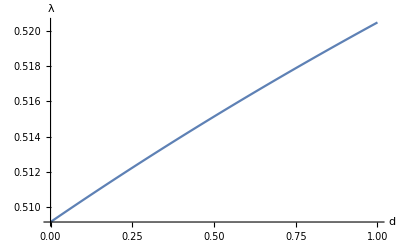

```mathematica
Plot[Evaluate[maxlambdainterval[[1]]],{d,0,1}, AxesLabel->{d,λ}]
```

Lemma 3.11 - λ_ub(a,d) - λ_lb(a,d) > 0 for all 0≤d≤1 and 0≤a<a_max(d). That is, a=a_max(d) is the only time at which λ_ub(a_max(d),d) = λ_lb(a_max(d),d) for 0<=a<=a_max(d).

As the λ_ub(a,d) and λ_lb(a,d) are continuous and defined everywhere, we can simply ask Mathematica to find all solutions when they are equivalent. We can then compare each solution to ensure it’s identical to our previous result of a_max(d). We can also check if λ_ub(0,d) and λ_lb(0,d) originally were different valued, using the fact that they only meet at a=a_max(d) and their continuousness to justify a positive difference between the two for all other values of a and d.

```mathematica
intersectiona =Reduce[goodcutscore==intsupcutscore &&goodcutscore==objparalcutscore&&0≤a<=maxa&&0≤lambda≤1&&0≤d≤1][[3]][[2]]
```

(-6767 √2-27068 √101+22220 √201-2680 √101 d+2020 √201 d)/(6767 √2-202 √201)

```mathematica
Assuming[0≤a≤maxa&&0≤d≤1&&0≤lambda≤1,Simplify[intersectiona==maxa]]
```

True

```mathematica
Assuming[0≤d≤1&&a==0,FullSimplify[lambdainterval[[5]]-lambdainterval[[1]]>0]]
```

True

For the below Lemma, we need to make a difference between the region R_GC and the function r_GC(a,d). The region exactly contains all tuples (a,d,λ) that result in GC being the best scoring cut. The function r_GC(a,d) is defined for all (a,d) ∈  × [0,1], and maps any pairing of (a,d) to the set of λ values contained in the region R_GC for the corresponding fixed (a,d) values.

Lemma 3.12 - An interval [λ_lb(a',d),  λ_ub(a',d)] ⊆ r_GC(a',d)  can be constructed, where  λ_ub(a',d) - λ_lb(a',d) > 0 for all 0≤d≤1 and 0≤a'< a_max(d).

This Lemma follows from some manipulation of our previous results, but here I’ll give some additional understanding. We have shown in Lemma 3.10 a plot for the values of λ_ub(a_max(d),d). We see how the end points aren’t the same, and we have shown that the function is continuous. This plot is the time at which λ_ub(a,d) and λ_lb(a,d) meet over the region R_GC. You can see this if you scroll up to Lemma 3.6 where we first plotted the region.So what we would like to do is to step back slightly from the end-point of the region R_GC (in the direction of a).  We have ensured that when we step back we have an interval of λ values, because we have shown that the upper and lower bounds only meet at a_max(d), and that the upper curve is strictly larger than the lower for all other values of 0 <= a < a_max(d). We have also shown that the bounds are continuous and defined everywhere. We can therefore take a small step (in the direction of a) back for different values of d, and we can be sure that our intervals won’t overlap! (We do not calculate the size of the step, but we know it exists)
This can be a bit confusing though, so here’s concretely what it means. A small interval of λ values has been constructed, and for only these λ values does the problem select GC and by extension solve to integer optimality. Moreover, we have shown that we can create an interval for all values of d, and that as the point we perturb from (perturb here means how much we step back in the direction of a from a = a_max(d)) changes continuously depending on d. So given a finite discretization of λ, we could construct infinitely many instances, where each instance only solves for some slightly different small λ interval (infinitely many possible values in the interval), where all the intervals lie between the discretization!  

ϵ̂ from the paper here is simply the variable eps

```mathematica
lambdaintervalwitheps = Simplify[lambdainterval/.a->maxa-eps]
```

(2 (606 (-32401+220 √20301)+120 d (-31411+211 √20301+10 (-151+√20301) d)+1/(101 (-195+2 √402))12 (101 (-110+√20301)+10 (-101+√20301) d) (-46359-11211 √402+808 √20301-10 (606+101 √402-8 √20301) d+4 √20301 √(101 (16192+109 √202-101 √402-109 √20301)+20 (15756+105 √202-101 √402-105 √20301) d+100 (152+√202-√402-√20301) d^2)+19695 eps-202 √402 eps)-1/(101 (195-2 √402)^2)6 (46359+11211 √402-808 √20301+10 (606+101 √402-8 √20301) d-4 √20301 √(101 (16192+109 √202-101 √402-109 √20301)+20 (15756+105 √202-101 √402-105 √20301) d+100 (152+√202-√402-√20301) d^2)-19695 eps+202 √402 eps)^2+√20301 √((101+d (20+d)+1/(10201 (195-2 √402)^2)(46359+11211 √402-808 √20301+10 (606+101 √402-8 √20301) d-4 √20301 √(101 (16192+109 √202-101 √402-109 √20301)+20 (15756+105 √202-101 √402-105 √20301) d+100 (152+√202-√402-√20301) d^2)-19695 eps+202 √402 eps)^2) (3272501-22220 √20301+20 d (31411-211 √20301-10 (-151+√20301) d)+1/(101 (-195+2 √402))2 (101 (-110+√20301)+10 (-101+√20301) d) (46359+11211 √402-808 √20301+10 (606+101 √402-8 √20301) d-4 √20301 √(101 (16192+109 √202-101 √402-109 √20301)+20 (15756+105 √202-101 √402-105 √20301) d+100 (152+√202-√402-√20301) d^2)-19695 eps+202 √402 eps)+1/(101 (195-2 √402)^2)(46359+11211 √402-808 √20301+10 (606+101 √402-8 √20301) d-4 √20301 √(101 (16192+109 √202-101 √402-109 √20301)+20 (15756+105 √202-101 √402-105 √20301) d+100 (152+√202-√402-√20301) d^2)-19695 eps+202 √402 eps)^2))))/(505 (-76409+528 √20301)+d (-7403300+50640 √20301+(-355633+2400 √20301) d)+1/(101 (-195+2 √402))24 (101 (-110+√20301)+10 (-101+√20301) d) (-46359-11211 √402+808 √20301-10 (606+101 √402-8 √20301) d+4 √20301 √(101 (16192+109 √202-101 √402-109 √20301)+20 (15756+105 √202-101 √402-105 √20301) d+100 (152+√202-√402-√20301) d^2)+19695 eps-202 √402 eps)+1/(101 (195-2 √402)^2)55 (46359+11211 √402-808 √20301+10 (606+101 √402-8 √20301) d-4 √20301 √(101 (16192+109 √202-101 √402-109 √20301)+20 (15756+105 √202-101 √402-105 √20301) d+100 (152+√202-√402-√20301) d^2)-19695 eps+202 √402 eps)^2)≤lambda≤(-73203+660 √402+60 (-220+√402-10 d) d-1/(101 (-195+2 √402))6 (-421+111 √402+10 (-2+√402) d) (46359+11211 √402-808 √20301+10 (606+101 √402-8 √20301) d-4 √20301 √(101 (16192+109 √202-101 √402-109 √20301)+20 (15756+105 √202-101 √402-105 √20301) d+100 (152+√202-√402-√20301) d^2)-19695 eps+202 √402 eps)+1/(10201 (195-2 √402)^2)3 (-203+2 √402) (46359+11211 √402-808 √20301+10 (606+101 √402-8 √20301) d-4 √20301 √(101 (16192+109 √202-101 √402-109 √20301)+20 (15756+105 √202-101 √402-105 √20301) d+100 (152+√202-√402-√20301) d^2)-19695 eps+202 √402 eps)^2+√402 √(-((101+d (20+d)+1/(10201 (195-2 √402)^2)(46359+11211 √402-808 √20301+10 (606+101 √402-8 √20301) d-4 √20301 √(101 (16192+109 √202-101 √402-109 √20301)+20 (15756+105 √202-101 √402-105 √20301) d+100 (152+√202-√402-√20301) d^2)-19695 eps+202 √402 eps)^2) (-24401+220 √402+20 (-220+√402-10 d) d-1/(101 (-195+2 √402))2 (-421+111 √402+10 (-2+√402) d) (46359+11211 √402-808 √20301+10 (606+101 √402-8 √20301) d-4 √20301 √(101 (16192+109 √202-101 √402-109 √20301)+20 (15756+105 √202-101 √402-105 √20301) d+100 (152+√202-√402-√20301) d^2)-19695 eps+202 √402 eps)+1/(10201 (195-2 √402)^2)(-203+2 √402) (46359+11211 √402-808 √20301+10 (606+101 √402-8 √20301) d-4 √20301 √(101 (16192+109 √202-101 √402-109 √20301)+20 (15756+105 √202-101 √402-105 √20301) d+100 (152+√202-√402-√20301) d^2)-19695 eps+202 √402 eps)^2))))/(-59669+660 √402+2 (-5260+30 √402-233 d) d-1/(101 (-195+2 √402))6 (-421+111 √402+10 (-2+√402) d) (46359+11211 √402-808 √20301+10 (606+101 √402-8 √20301) d-4 √20301 √(101 (16192+109 √202-101 √402-109 √20301)+20 (15756+105 √202-101 √402-105 √20301) d+100 (152+√202-√402-√20301) d^2)-19695 eps+202 √402 eps)+1/(10201 (195-2 √402)^2)(-475+6 √402) (46359+11211 √402-808 √20301+10 (606+101 √402-8 √20301) d-4 √20301 √(101 (16192+109 √202-101 √402-109 √20301)+20 (15756+105 √202-101 √402-105 √20301) d+100 (152+√202-√402-√20301) d^2)-19695 eps+202 √402 eps)^2)

To this point in the notebook, we have assumed that the LP optimal point is where we wanted it to be. We have shown that the cuts scoring are always valid, that the cuts always cut off the previous facet created, and that we can construct a controllable interval of λ values to trick the solver. However, this has been under the assumption that our original LP optimal solution is non-integer, and that after applying GC our problem is solved, and that after applying ISC^n or OPC^n our new solution lies on a newly created facet. We now show that the assumptions thus far have been correct, given our bounds on 0≤a≤a_max(d) and 0≤d≤1.

Lemma 3.13 - The fractional solution (-1/2,3,1/2)  is LP optimal for P(a,d) for all 0≤d≤1 and 0≤a≤a_max(d).

We show this by verifying that the objective at  (-1/2,3,1/2) is less than at any of the other vertices from the original problem before cuts have been applied.

```mathematica
initlp = {x1->-1/2,x2->3,x3->1/2};
Assuming[0≤d≤1&&0≤a≤maxa,FullSimplify[Reduce[Evaluate[objective/.initlp]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.initlp]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.initlp]<Evaluate[objective/.integerpoints[[3]]]]]]
```

False

Lemma 3.14 - The integer solution (1,1,0) is LP optimal after applying GC to P(a,d) for all 0≤d≤1 and 0≤a≤a_max(d).

We show this verifying that the objective at (1,1,0) is less than at any other vertex when GC  is applied.

```mathematica
objective = x1-(10+d)x2-a*x3;
Assuming[0≤d≤1&&0≤a≤maxa,FullSimplify[Reduce[Evaluate[objective/.integerpoints[[3]]]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.integerpoints[[3]]]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.integerpoints[[3]]]<Evaluate[objective/.goodv1]]]]
```

True

Lemma 3.15 - Having applied the cut ISC^n to P(a,d), a point from (ISC^n)_x\ I_x is LP optimal for all 0≤d≤1 and 0≤a≤a_max(d).

This follows the same procedure as above, but we now need to simply verify that at-least one point on the newly created facet is LP optimal.

```mathematica
intsupintv1 = Evaluate[objective/.intsupv1]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.intsupv1]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.intsupv1]<Evaluate[objective/.integerpoints[[3]]];
intsupintv2 = Evaluate[objective/.intsupv2]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.intsupv2]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.intsupv2]<Evaluate[objective/.integerpoints[[3]]];
intsupintv3 = Evaluate[objective/.intsupv3]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.intsupv3]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.intsupv3]<Evaluate[objective/.integerpoints[[3]]];
Assuming[0≤d≤1&&0≤a≤maxa&&0≤10eps≤1,FullSimplify[intsupintv1||intsupintv2||intsupintv3]]
```

True

As above, we repeat the procedure but for OPC^n
Lemma 3.16 - Having applied the cut OPC^n to P(a,d), a point from (OPC^n)_x\ I_x is LP optimal for all 0≤d≤1 and 0≤a≤a_max(d)

```mathematica
objparalintv1 =  Evaluate[objective/.objparalv1]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.objparalv1]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.objparalv1]<Evaluate[objective/.integerpoints[[3]]];
objparalintv2 =  Evaluate[objective/.objparalv2]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.objparalv2]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.objparalv2]<Evaluate[objective/.integerpoints[[3]]];
objparalintv3 =  Evaluate[objective/.objparalv3]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.objparalv3]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.objparalv3]<Evaluate[objective/.integerpoints[[3]]];
Assuming[0≤d≤1&&0≤a≤maxa&&0≤10eps≤1,FullSimplify[objparalintv1||objparalintv2||objparalintv3]]
```

True

Theorem 3.1 - Given a finite discretization of λ, an infinite family of MILP instances together with an infinite amount of family-wide valid cuts can can be constructed. Using a pure cutting plane approach and applying a single cut per selection round, the infinite family of instances do not solve to optimality for any value in the discretization, but do solve to optimality for an infinite amount of alterative λ values.

We now have all the tools we need to prove this theorem! 

From Lemmas 3.2 - 3.5, we know the exact vertex set of our feasible region at each stage of the solving process, as well as the exact set of cuts at each round. Furthermore, as at each round only the RHS value for each proposed cut changes, the scoring of the cuts at each new round remains constant, and we can therefore completely describe the three scenarios of how cuts would be added. 

The three scenarios are:
Just GC has been added (and the problem then solved)
An infinite amount of ISC^n cuts have been added (and the problem never solved)
An infinite amount of OPC^n cuts have been added (and the problem never solved)

From Lemma 3.6 we know the sufficient conditions for a λ value that results in GC being scored at-least as well as the other cuts. Lemmas 3.7 - 3.11 show how these sufficient conditions can be used to construct the region R_GC. Moreover, they show that R_GC is bounded, and that a=a_max(d) is the only time at which λ_ub(a_max(d),d) = λ_lb(a_max(d),d) for all 0 <=d<=1.

We therefore conclude that R_GC is connected. We know from Lemma 3.10 that both λ_ub(a_max(d),d)  and λ_lb(a_max(d),d) are continuous, where 0<=d<=1, and that λ_ub(a_max(1),1) > λ_ub(a_max(0),0). From the intermediate value theorem, we then know the following:
										∀λ ∈ [ λ_ub(a_max(0),0) = λ_lb(a_max(1),1)],    ∃  d’ s.t  λ = λ_ub(a_max(d'),d')    (28)
From Lemma 3.12 we have shown an explicit way to use this information to construct an interval [λ_lb(a_max(d)-ϵ̂,d),  λ_ub(a_max(d)-ϵ̂,d)] ⊆  r_GC(a,d) for all (a,d, ϵ̂) ∈ [0, a_max(d)) ×[0,1] ×(0,a]. These intervals can be arbitrarily small as ϵ̂ can be arbitrarily small, and λ_ub(a_max(d),d) and λ_lb(a_max(d),d) are continuous polynomials defined over the entire domain, where λ_ub(a_max(d),d) = λ_lb(a_max(d),d). 
Moreover, as d’ from above can be used, and λ_ub(a_max(d),d), λ_lb(a_max(d),d), and a_max(d) are polynomials, we can generate infinitely many disjoint intervals. We can therefore conclude that for any finite discretization of λ, an interval can be created that contains no values from the discretization, but contains an infinite amount of λ values for which GC is applied and P(a,d) solved to integer optimality.

To think of this geometrically, go back to Lemma 3.6 and look at the region R_GC. The endpoints of the region at a= a_max(d) are not all equal (which we visualised in Lemma 3.8 when  λ_ub(a_max(1),1) > λ_lb(a_max(0),0)). We also concluded above that there is a d’ that makes the endpoints of the region at a= a_max(d) equal for any  λ ∈ [ λ_ub(a_max(0),0) = λ_lb(a_max(1),1)]. These endpoints are the only time when λ_ub(a,d) = λ_lb(a,d) as well. So if we walk back slightly, to a point  a=a_max(d)-ϵ̂, we get an interval that contains more than a single point when we use the interval construction from Lemma 3.12. Because  λ_ub(a,d) and λ_lb(a,d) are polynomials of a bounded degree, we also know that slightly perturbing the input does not lead to an insane jump of a different value. So for any d, we slightly walk back the value of a to a=a_max(d)-ϵ̂, and we can construct an interval of λ values that will select GC while all others values of λ lead to ISC^nor OPC^n being selected and an infinite amount of cuts applied. 
The boundaries of the interval [λ_ub(a,d), λ_lb(a,d)], are both function evaluations. The perturbations of their input can be made arbitrarily small (via ϵ̂), and the function evaluation difference to that of the original input is polynomially bounded due to the functions being polynomials and defined over the domain. The difference of the function evaluations can therefore also be made arbitrarily small. 
So we have that arbitrarily small intervals can be created, where the boundary values of each interval are different perturbations of  λ ∈ [ λ_ub(a_max(0),0) = λ_lb(a_max(1),1)]. As we can construct an infinite amount of disjoint intervals (start from different points and use sufficiently small perturbations),  no finite discretization can guarantee to be contain a λ value from every such interval.

Finally, Lemmas 3.13 - 3.16 ensure that each stage of the solving process, all cuts are valid for any non-integer feasible LP optimal solution for all P(a,d),[0, a_max(d)) ×[0,1]. Moreover, the Lemmas guarantee that only after applying GC is an integer optimal solution found. 

We therefore have shown how fixing a global value of λ to a constant for use in the MILP solving process while disregarding all instance information can result in infinitely worse performance for infinitely many instances.

Corollary 3.1.1 - There exists an infinite family of MILP instances together with an infinite amount of family-wide valid cuts, which do not solve to integer optimality for any λ when using a pure cutting plane approach and applying a single cut per selection round.

To show this we take the following function, where 0≤d≤1:
	\hat{a_max(d,ϵ)} = a_max(d) + ϵ,     where 0<ϵ≤0.1

Any such value of a retrieved from this function will lie outside of  R_GC, as a_max(d) was the maximum value of a over the region. There thus would exist no λ value that results in finite termination, as GC is never scored at-least as high as the other cuts. 

Similar to Theorem 3.1, we need to ensure that the LP optimal point at all times during the solving process is appropriate, and that the same integer optimal point stays integer optimal for all 0≤d≤1 and a_max(d) < \hat{a_max(d,ϵ)} ≤  a_max(d) + 0.1. We therefore redo the proofs of Lemmas 3.13 - 3.16 but with a new domain of a.

```mathematica
Assuming[0≤d≤1&&maxa<a≤maxa+1/10,FullSimplify[Reduce[Evaluate[objective/.initlp]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.initlp]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.initlp]<Evaluate[objective/.integerpoints[[3]]]]]]
```

True

```mathematica
Assuming[0≤d≤1&&max<a≤maxa+1/10,FullSimplify[Reduce[Evaluate[objective/.integerpoints[[3]]]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.integerpoints[[3]]]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.integerpoints[[3]]]<Evaluate[objective/.goodv1]]]]
```

True

```mathematica
intsupintv1 = Evaluate[objective/.intsupv1]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.intsupv1]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.intsupv1]<Evaluate[objective/.integerpoints[[3]]];
intsupintv2 = Evaluate[objective/.intsupv2]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.intsupv2]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.intsupv2]<Evaluate[objective/.integerpoints[[3]]];
intsupintv3 = Evaluate[objective/.intsupv3]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.intsupv3]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.intsupv3]<Evaluate[objective/.integerpoints[[3]]];
Assuming[0≤d≤1&&maxa<a≤maxa+1/10&&0≤10eps≤1,FullSimplify[intsupintv1||intsupintv2||intsupintv3]]
```

True

```mathematica
objparalintv1 =  Evaluate[objective/.objparalv1]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.objparalv1]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.objparalv1]<Evaluate[objective/.integerpoints[[3]]];
objparalintv2 =  Evaluate[objective/.objparalv2]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.objparalv2]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.objparalv2]<Evaluate[objective/.integerpoints[[3]]];
objparalintv3 =  Evaluate[objective/.objparalv3]<Evaluate[objective/.integerpoints[[1]]]&&Evaluate[objective/.objparalv3]<Evaluate[objective/.integerpoints[[2]]]&&Evaluate[objective/.objparalv3]<Evaluate[objective/.integerpoints[[3]]];
Assuming[0≤d≤1&&maxa≤a≤maxa+1/10&&0≤10eps≤1,FullSimplify[objparalintv1||objparalintv2||objparalintv3]]
```

True